```mathematica
Remove["Global`*"]
```

```mathematica
DSolve[{D[f[x], x,x]-x*f[x]==0}, f[x],x]
```

{{f[x]→AiryAi[x] C[1]+AiryBi[x] C[2]}}

```mathematica
DSolve[{D[f[x], x,x]-x*f[x]==0, f[∞]==0, f[-E/(mgl)]==0}, f[x], x]
```

{{f[x]→0}}

```mathematica
DSolve[{D[f[x], x,x]-x*f[x]==0, f[∞]==0}, f[x], x]
```

DSolve::bvsing: Unable to resolve some of the arbitrary constants in the general solution using the given boundary conditions. It is possible that some of the conditions have been specified at a singular point for the equation.

{{f[x]→AiryAi[x] C[1]}}

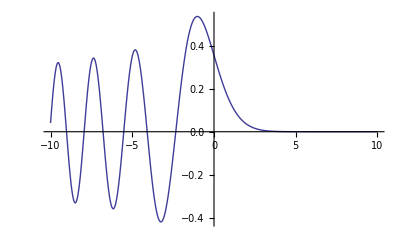

```mathematica
Plot[AiryAi[x],{x,-10,10}]
```

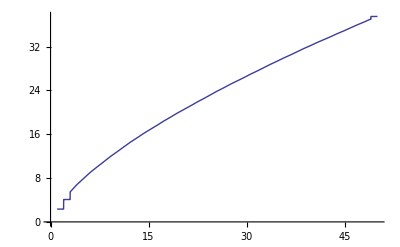

```mathematica
Plot[-N[AiryAiZero[Floor[k]]],{k,0,50}]
```

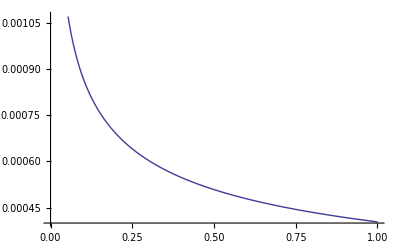

```mathematica
Plot[N[AiryAiZero[Floor[k]]]-N[AiryAiZero[Floor[k+1]]],{k,1,10^11}]
```